```mathematica
data={{0,89.5,0.8344,400,35132.147,0.004},{1,86.1,1.189,495,37486,0.213},{2,72.5,2.025,453,40850,0.408},{3,84.9,1.252,437,42334,0.451},{4,49.0,2.960,432,43008,0.469},{5,71,1.490,483,41820,0.143},{6,82.8,2.039,433,42070,0.16},{7,93.0,1.862,428,32801,0.174},{8,87.0,2.222,374,43025,0.179},{9,89.9,1.470,373,43882,0.199},{10,86.9,1.783,364,44016,0.201},{11,100.0,2.094,361,44950,0.22},{12,85.0,2.297,355,45270,0.23},{13,91.6,2.705,350,45650,0.244},{14,108.5,2.123,347,46050,0.25},{15,110.6,0.9929,343,46370,0.254},{16,109.2,2.637,339,46680,0.262},{17,103.4,2.545,332,47100,0.266},{18,106.3,2.742,328,48700,0.285},{19,108.4,2.945,324,49500,0.292},{20,110.8,3.143,219,49820,0.302},{21,113.7,3.057,372,49445.135,0.280},{22,118.1,3.453,369,49799.44,0.289},{23,117.8,3.924,367,49922.022,0.292},{24,124.9,3.879,365,50161.21,0.297},{25,114.8,3.714,361,50525.289,0.305},{26,130.5,3.527,354,50885.237,0.312},{27,121.2,4.735,352,51696.298,0.324},{28,129.5,6.093,342,53607.162,0.335},{29,129.2,4.313,334,54584.194,0.346},{30,135.7,4.991,338,54664.037,0.371},{31,138.3,4.798,332,54700.803,0.344},{32,144.8,6.136,328,55471.001,0.351},{33,146.5,4.922,324,56155.978,0.367},{34,152.8,3.769,321,56890.635,0.370},{35,157.9,4.696,318,57062.782,0.372},{36,150.6,5.331,316,57520.537,0.381},{37,134.1,5.191,312,58758.544,0.388},{38,142.3,5.431,313,58333.626,0.401},{39,149.6,5.986,311,58889.273,0.412},{40,152.1,6.318,313,58819.638,0.422},{41,156.5,5.033,309,59875.573,0.434},{42,174.0,4.858,306,60012.439,0.435},{43,166.0,7.154,303,60469.542,0.448},{44,165.0,8.850,301,61385.012,0.452},{45,164.4,4.934,297,62068.634,0.461},{46,158.6,6.373,293,62462.423,0.465},{47,154.5,4.092,291,62863.728,0.473},{48,144.9,8.761,288,63658.026,0.488},{49,172.8,4.834,287,64136.861,0.493},{50,181.0,5.803,232,65700,0.536},{51,204.5,5.762,231,66457,0.535},{52,208.4,6.216,229,66564,0.543},{53,212.0,5.819,226,66634.22,0.533},{54,213.2,6.012,226,69119.920,0.550},{55,216.8,6.582,225,69038.856,0.557},{56,221.9,6.472,222,68550.328,0.559},{57,225.8,6.208,220,69683.158,0.568},{58,228.4,6.420,217,70505.9,0.571},{59,231.4,6.276,215,69605.859,0.589},{60,233.4,6.306,213,70855.864,0.603},{61,237.2,6.294,212,71954.75,0.610},{62,238.6,6.385,210,72583.666,0.615},{63,241.7,6.634,208,72565.252,0.621},{64,243.7,6.534,210,72764.173,0.626},{65,247.3,6.583,207,73350.179,0.639},{66,250.4,6.626,206,73667.279,0.673},{67,254.5,6.499,210,74036.935,0.678},{68,256.1,6.763,211,74546.25,0.675},{69,258.2,6.702,206,75905.966,0.772},{70,179.3,5.996,204,77431.161,0.784},{71,215.1,5.688,241,77081.339,0.704},{72,252.4,7.475,235,77095.318,0.708},{73,255.2,7.424,234,78512.565,0.732},{74,263.1,7.363,233,79193.381,0.753},{75,266.6,7.544,228,80757.477,0.801},{76,268.0,7.459,224,82842.43,0.840},{77,270.5,7.113,220,82744.254,0.840},{78,273.6,7.872,219,83908.467,0.848},{79,277.2,7.454,215,85829.529,0.850},{80,279.0,7.510,212,86327.636,0.846},{81,281.1,7.546,211,87063.809,0.858},{82,285.3,7.429,210,87764.648,0.862},{83,286.6,7.880,208,89036.206,0.865},{84,291.1,7.578,208,88383.408,0.867},{85,293.4,7.781,206,89184.064,0.858},{86,294.9,7.903,204,89963.312,0.868},{87,295.7,7.842,203,90342.628,0.866},{88,297.4,7.886,202,91270.112,0.872},{89,303.6,8.098,200,92767.773,0.874},{90,313.9,7.686,200,92808.262,0.878},{91,312.9,7.951,197,93586.318,0.874},{92,314.2,7.980,195,95211.781,0.882},{93,317.7,7.992,194,94823.477,0.875},{94,322.7,8.222,192,95427.889,0.877},{95,324.3,8.122,191,96382.883,0.882},{96,327.2,8.268,190,97512.059,0.877},{97,329.5,8.313,188,98066.34,0.880},{98,332.7,8.277,187,98427.538,0.882},{99,335.7,8.434,185,99034.261,0.882},{100,335.4,8.623,180,102584.497,0.882},{101,336.1,8.589,177,103141.502,0.885},{102,340,8.906,176,104110.959,0.887},{103,341.3,8.875,174,105461.491,0.889},{104,345.6,8.835,173,105806.233,0.890},{105,346.2,8.712,171,104867.615,0.892},{106,350.2,9.011,169,107401.499,0.894},{107,353.1,9.003,168,108077.396,0.893},{108,355.3,9.015,167,109046.999,0.896},{109,358.1,9.059,166,109381.367,0.895},{110,359.6,9.128,163,110243.441,0.894},{111,363.9,9.305,167,111285.209,0.902},{112,367.6,9.331,165,112572.665,0.902},{113,369.7,9.295,161,113506.747,0.905},{114,372.9,9.362,160,114287.953,0.903},{115,376.4,9.189,158,114868.601,0.906},{116,377.5,9.319,157,116015.962,0.904},{117,378.8,9.277,158,116014.939,0.907},{118,384.7,9.257,157,117082.131,0.909}};

capacitance=data[[All, {1, 2}]];
frequency=data[[All, {1, 4}]];
time=data[[All, {1, 5}]];
compensated=data[[All, {1, 6}]];

(* 
	Capacitância 
*)
plot=ListPlot[capacitance, Joined->True, AxesLabel->{"Volume (mL)", "Capacitância (pF)"}, PlotLabel->"Função de Transferência Experimental - Capacitância", ImageSize->Full];
Export[NotebookDirectory[]<>"/Images/Nivel/Experimental/Capacitancia.pdf",plot];

model=NonlinearModelFit[capacitance, a+m V, {a, m}, V];
Normal[model]
model["RSquared"]
capacitanceModel=model;

D[model[V], V]

plot=Show[Plot[model[V], {V, Min[capacitance[[All,1]]], Max[capacitance[[All,1]]]},AxesLabel->{"Volume (mL)", "Capacitância (pF)"}, PlotLabel->"Função de Transferência Experimental Ajustada - Capacitância", ImageSize->Full],
ListPlot[capacitance, AxesLabel->{"Volume (mL)", "Capacitância (pF)"}, PlotLabel->"Função de Transferência Experimental - Capacitância", ImageSize->Full, PlotStyle->Orange]
];
Export[NotebookDirectory[]<>"/Images/Nivel/Experimental/Capacitancia-Ajuste.pdf",plot];

(* 
	Frequência 
*)
plot=ListPlot[frequency, Joined->True, AxesLabel->{"Volume (mL)", "Frequência (Hz)"}, PlotLabel->"Função de Transferência Experimental - Frequência", ImageSize->Full];
Export[NotebookDirectory[]<>"/Images/Nivel/Experimental/Frequencia.pdf",plot];

model=NonlinearModelFit[frequency, a+m V, {a, m}, V];
Normal[model]
model["RSquared"]
frequencyModel=model;

D[model[V], V]

plot=Show[Plot[model[V], {V, Min[frequency[[All,1]]], Max[frequency[[All,1]]]},AxesLabel->{"Volume (mL)", "Frequência (Hz)"}, PlotLabel->"Função de Transferência Experimental Ajustada - Frequência", ImageSize->Full],
ListPlot[frequency, AxesLabel->{"Volume (mL)", "Frequência (Hz)"}, PlotLabel->"Função de Transferência Experimental - Frequência", ImageSize->Full, PlotStyle->Orange]
];
Export[NotebookDirectory[]<>"/Images/Nivel/Experimental/Frequencia-Ajuste.pdf",plot];


(* 
	Ciclos 
*)
plot=ListPlot[time, Joined->True, AxesLabel->{"Volume (mL)", "Ciclos"}, PlotLabel->"Função de Transferência Experimental - Ciclos", ImageSize->Full];
Export[NotebookDirectory[]<>"/Images/Nivel/Experimental/Ciclos.pdf",plot];

model=NonlinearModelFit[time, a+m V, {a, m}, V];
Normal[model]
model["RSquared"]
timeModel=model;

D[model[V], V]

plot=Show[Plot[model[V], {V, Min[time[[All,1]]], Max[time[[All,1]]]},AxesLabel->{"Volume (mL)", "Ciclos"}, PlotLabel->"Função de Transferência Experimental Ajustada - Ciclos", ImageSize->Full],
ListPlot[time, AxesLabel->{"Volume (mL)", "Ciclos"}, PlotLabel->"Função de Transferência Experimental - Ciclos", ImageSize->Full, PlotStyle->Orange]
];
Export[NotebookDirectory[]<>"/Images/Nivel/Experimental/Ciclos-Ajuste.pdf",plot];

(* 
	Compensado 
*)
plot=ListPlot[compensated, Joined->True, AxesLabel->{"Volume (mL)", "Compensado"}, PlotLabel->"Função de Transferência Experimental - Compensado", ImageSize->Full];
Export[NotebookDirectory[]<>"/Images/Nivel/Experimental/Compensado.pdf",plot];

model=NonlinearModelFit[compensated, a+b V+ c Power[V,2], {a, b, c}, V];
Normal[model]
model["RSquared"]
compensatedModel=model;

D[model[V], V]

plot=Show[Plot[model[V], {V, Min[compensated[[All,1]]], Max[compensated[[All,1]]]},AxesLabel->{"Volume (mL)", "Compensado"}, PlotLabel->"Função de Transferência Experimental Ajustada - Compensado", ImageSize->Full],
ListPlot[compensated, AxesLabel->{"Volume (mL)", "Compensado"}, PlotLabel->"Função de Transferência Experimental - Compensado", ImageSize->Full, PlotStyle->Orange]
];
Export[NotebookDirectory[]<>"/Images/Nivel/Experimental/Compensado-Ajuste.pdf",plot];
```

57.3962+2.75376 V

0.99716

2.75376

394.095-2.24631 V

0.988086

-2.24631

34409.2+658.776 V

0.998731

658.776

0.133032+0.00898593 V-0.0000148452 V^2

0.989612

0.00898593-0.0000296905 V

```mathematica
Map[({#1[[1]],SetAccuracy[PlusMinus[#1[[2]],#1[[2]]*0.03//N],1]})&, time];
Grid[%]//TeXForm;
```

```mathematica
FindIdealityError[input_, function_]:=(
Max[Map[Abs[function[#1[[1]]]-#1[[2]]+input[[1, 2]]]&, input]]/Max[input[[All,2]]]
);
```

((700.035 h+8.85 H) EllipticK[√(1-d^4/(16 (d+w)^4))])/EllipticK[1/2 √(d^2/(d+w)^2)]

{3.41655,36.7807,53.4627,70.1448,86.8268,103.509,120.191,136.873,153.555,170.237}

0.36314 (-57.3962+1. C)

3.41655+1.66821 V

1.66821

3.41655+2001.85 h

2.00185

Erro de Linearidade = 100 FindIdealityError[{{0,89.5},{1,86.1},{2,72.5},{3,84.9},{4,49.},{5,71},{6,82.8},{7,93.},{8,87.},{9,89.9},{10,86.9},{11,100.},{12,85.},{13,91.6},{14,108.5},{15,110.6},{16,109.2},{17,103.4},{18,106.3},{19,108.4},{20,110.8},{21,113.7},{22,118.1},{23,117.8},{24,124.9},{25,114.8},{26,130.5},{27,121.2},{28,129.5},{29,129.2},{30,135.7},{31,138.3},{32,144.8},{33,146.5},{34,152.8},{35,157.9},{36,150.6},{37,134.1},{38,142.3},{39,149.6},{40,152.1},{41,156.5},{42,174.},{43,166.},{44,165.},{45,164.4},{46,158.6},{47,154.5},{48,144.9},{49,172.8},{50,181.},{51,204.5},{52,208.4},{53,212.},{54,213.2},{55,216.8},{56,221.9},{57,225.8},{58,228.4},{59,231.4},{60,233.4},{61,237.2},{62,238.6},{63,241.7},{64,243.7},{65,247.3},{66,250.4},{67,254.5},{68,256.1},{69,258.2},{70,179.3},{71,215.1},{72,252.4},{73,255.2},{74,263.1},{75,266.6},{76,268.},{77,270.5},{78,273.6},{79,277.2},{80,279.},{81,281.1},{82,285.3},{83,286.6},{84,291.1},{85,293.4},{86,294.9},{87,295.7},{88,297.4},{89,303.6},{90,313.9},{91,312.9},{92,314.2},{93,317.7},{94,322.7},{95,324.3},{96,327.2},{97,329.5},{98,332.7},{99,335.7},{100,335.4},{101,336.1},{102,340},{103,341.3},{104,345.6},{105,346.2},{106,350.2},{107,353.1},{108,355.3},{109,358.1},{110,359.6},{111,363.9},{112,367.6},{113,369.7},{114,372.9},{115,376.4},{116,377.5},{117,378.8},{118,384.7}},theoricalCapacitance[(5 #1)/6000]&]

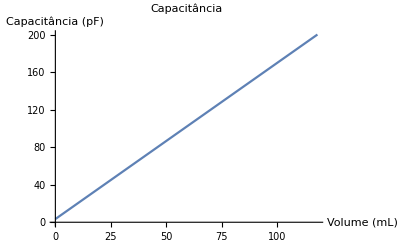

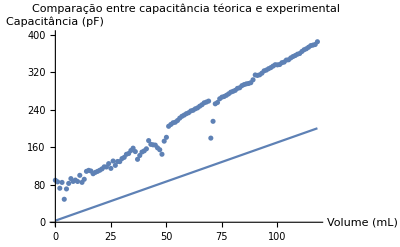

```mathematica
CoplanarStripsCapacitance[ϵ_,L_,d_,w_]:= ϵ L EllipticK[Sqrt[1-Power[d^2/(4 (d+w) (d+w)), 2]]]/EllipticK[1/2 √(d^2/((d+w) (d+w)))];
FullSimplify[(CoplanarStripsCapacitance[8.85 10^-12 ,H-h, d,w ]+CoplanarStripsCapacitance[80.1*8.85 10^-12 , h, d,w])/10^-12]


theoricalCapacitance[H_]=(CoplanarStripsCapacitance[8.85 10^-12 ,135/1000-H, 14/1000,18/1000 ]+CoplanarStripsCapacitance[80.1*8.85 10^-12, H, 14/1000,18/1000])/10^-12;
theoricalCapacitance[5V/6000]/.V->{0, 20,30, 40,50,60,70,80,90,100}

Expand[theoricalCapacitance[5V/6000]//N]
D[theoricalCapacitance[5V/6000],V]

Expand[theoricalCapacitance[h]//N]
D[theoricalCapacitance[h/1000],h]

Print["Erro de Linearidade = ", FindIdealityError[capacitance, theoricalCapacitance[5#/6000]&]*100]

plot=Show[
Plot[theoricalCapacitance[5V/6000], {V, 0, 118}],
AxesLabel->{"Volume (mL)", "Capacitância (pF)"},
PlotLabel->"Capacitância", ImageSize->Full
]
Export[NotebookDirectory[]<>"/Images/Nivel/Teorico/Capacitancia.pdf",plot];

plot=Show[
Plot[theoricalCapacitance[5V/6000], {V, 0, 118}],
 ListPlot[capacitance],PlotRange->{0, 400},
AxesLabel->{"Volume (mL)", "Capacitância (pF)"},
PlotLabel->"Comparação entre capacitância téorica e experimental", ImageSize->Full
]
Export[NotebookDirectory[]<>"/Images/Nivel/Experimental/Capacitancia-Comparacao.pdf",plot];
```

8768.36+577084. h

577.084

8768.36+480.903 V

480.903

Erro de Linearidade = 14.0372

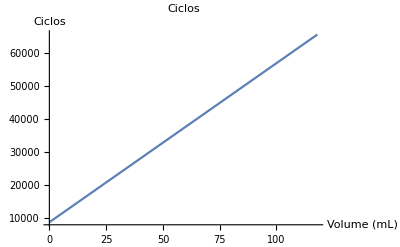

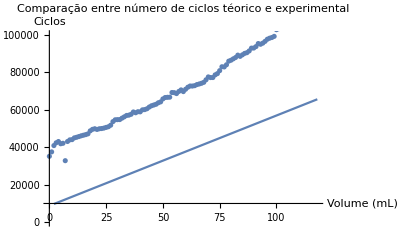

```mathematica
theoreticalTime[h_]=2 R Ca Log[(1+λ)/(1-λ)]*16000000/.{Ca->(theoricalCapacitance[h]+27) 10^-12, λ->10000/(10000+10000), R->(2200000+6000000)};
FullSimplify[theoreticalTime[h]]
D[theoreticalTime[h/1000], h]

FullSimplify[theoreticalTime[5V/6000]]
D[theoreticalTime[5V/6000], V]

Print["Erro de Linearidade = ", FindIdealityError[time, theoreticalTime[5#/6000]&]*100]

plot=Show[
Plot[theoreticalTime[5V/6000], {V, 0, 118}],
AxesLabel->{"Volume (mL)", "Ciclos"},
PlotLabel->"Ciclos", ImageSize->Full
]
Export[NotebookDirectory[]<>"/Images/Nivel/Teorico/Ciclos.pdf",plot];

plot=Show[
Plot[theoreticalTime[5V/6000], {V, 2, 118}],
 ListPlot[time],PlotRange->{0,100000},
AxesLabel->{"Volume (mL)", "Ciclos"},
PlotLabel->"Comparação entre número de ciclos téorico e experimental", ImageSize->Full
]
Export[NotebookDirectory[]<>"/Images/Nivel/Experimental/Ciclos-Comparacao.pdf",plot];
```

27.7256/(0.0151942+1. h)

33270.7/(18.2331+1. V)

-33270.7/(18.2331+1. V)^2

Erro de Linearidade = 368.635

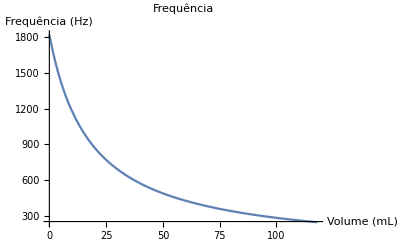

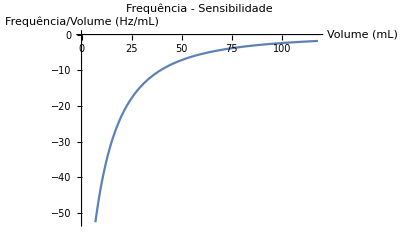

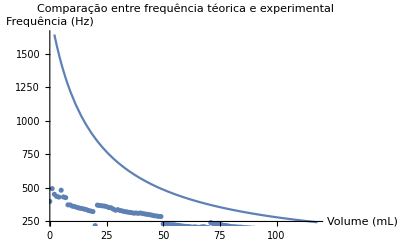

```mathematica
theoreticalFrequency[h_]=1/(2 R Ca Log[(1+λ)/(1-λ)])/.{Ca->(theoricalCapacitance[h]+27) 10^-12, λ->10000/(10000+10000), R->(2200000+6000000)};
FullSimplify[theoreticalFrequency[h]]
FullSimplify[theoreticalFrequency[5V/6000]]
sens=FullSimplify[D[theoreticalFrequency[5V/6000], V]]

Print["Erro de Linearidade = ", FindIdealityError[frequency, theoreticalFrequency[5#/6000]&]*100]

plot=Show[
Plot[theoreticalFrequency[5V/6000], {V, 0, 118}],
AxesLabel->{"Volume (mL)", "Frequência (Hz)"},
PlotLabel->"Frequência", ImageSize->Full
]
Export[NotebookDirectory[]<>"/Images/Nivel/Teorico/Frequencia.pdf",plot];

plot=Show[
Plot[sens, {V, 0, 118}],
AxesLabel->{"Volume (mL)", "Frequência/Volume (Hz/mL)"},
PlotLabel->"Frequência - Sensibilidade", ImageSize->Full
]
Export[NotebookDirectory[]<>"/Images/Nivel/Teorico/Frequencia-Sensibilidade.pdf",plot];


plot=Show[
Plot[theoreticalFrequency[5V/6000], {V, 2, 118}],
 ListPlot[frequency],
AxesLabel->{"Volume (mL)", "Frequência (Hz)"},
PlotLabel->"Comparação entre frequência téorica e experimental", ImageSize->Full
]
Export[NotebookDirectory[]<>"/Images/Nivel/Experimental/Frequencia-Comparacao.pdf",plot];
```

```mathematica
theoreticalCompensated[h_]=(Ca-Ca0)/(CR-Ce)/.{Ca->(theoricalCapacitance[h]+27) 10^-12,Ca0->(theoricalCapacitance[0]+27) 10^-12, CR->CoplanarStripsCapacitance[80.1 8.85 10^-12,270/1000, 14/1000,18/1000 ]+(27) 10^-12,
Ce->CoplanarStripsCapacitance[8.85 10^-12,27/1000, 14/1000,18/1000 ]+(27) 10^-12};
FullSimplify[theoreticalCompensated[h]]
FullSimplify[theoreticalCompensated[5V/6000]]
FullSimplify[D[theoreticalCompensated[5V/6000], V]]

Print["Erro de Linearidade = ", FindIdealityError[compensated, theoreticalCompensated[5#/6000]&]*100]

plot=Show[
Plot[theoreticalCompensated[5V/6000], {V, 0, 118}],
AxesLabel->{"Volume (mL)", "Valor N (Compensado)"},
PlotLabel->"Valor N (Compensado)", ImageSize->Full
];
Export[NotebookDirectory[]<>"/Images/Nivel/Teorico/Compensado.pdf",plot];

plot=Show[
Plot[theoreticalCompensated[5V/6000], {V, 0, 118}],
 ListPlot[compensated],
AxesLabel->{"Volume (mL)", "Valor N"},
PlotLabel->"Comparação entre o valor N compensado téorico e experimental", ImageSize->Full
];
Export[NotebookDirectory[]<>"/Images/Nivel/Experimental/Compensado-Comparacao.pdf",plot];

theoreticalCompensatedForTime=V/.Solve[compensatedModel[V]==(2 R Ca Log[(1+R1/(R1+R2))/(1-R1/(R1+R2))]*Clk-2 R Ca0 Log[(1+R1/(R1+R2))/(1-R1/(R1+R2))]*Clk)/(2 R CR Log[(1+R1/(R1+R2))/(1-R1/(R1+R2))]*Clk-2 R Ce Log[(1+R1/(R1+R2))/(1-R1/(R1+R2))]*Clk), V][[1]];

(*(theoreticalCompensatedForTime*Sqrt[Total[
{
Power[D[theoreticalCompensatedForTime, R]*R*0.1, 2],
Power[D[theoreticalCompensatedForTime, Ca]*Ca*0.01, 2],Power[D[theoreticalCompensatedForTime, R1]*R1*0.1, 2],Power[D[theoreticalCompensatedForTime, R2]*R2*0.1, 2],Power[D[theoreticalCompensatedForTime, Clk]*Clk*0.04, 2],Power[D[theoreticalCompensatedForTime, Ca0]*Ca0*0.01, 2],Power[D[theoreticalCompensatedForTime, CR]*CR*0.01, 2],Power[D[theoreticalCompensatedForTime, Ce]*Ce*0.01, 2]
}
]
]//FullSimplify)

(Sqrt[Total[
{
Power[D[theoreticalCompensatedForTime, R]*0.1, 2],
Power[D[theoreticalCompensatedForTime, Ca]*0.01, 2],Power[D[theoreticalCompensatedForTime, R1]*0.1, 2],Power[D[theoreticalCompensatedForTime, R2]*0.1, 2],Power[D[theoreticalCompensatedForTime, Clk]*0.04, 2],Power[D[theoreticalCompensatedForTime, Ca0]*0.01, 2],Power[D[theoreticalCompensatedForTime, CR]*0.01, 2],Power[D[theoreticalCompensatedForTime, Ce]*0.01, 2]
}
]
]//FullSimplify)/.{R->2200000, Ca->capacitance[[All, 2]], R1->10000, R2->10000, Clk->16000000, Ca0->89.5 10^-12, CR->89.5 10^-12, Ce->600 10^-12}//N*)


theoreticalCompensatedForTime=V/.Solve[compensatedModel[V]==(T-T0)/(TR-TRE), V][[1]];
(Sqrt[Total[
{
Power[D[theoreticalCompensatedForTime, T]*0.03, 2],
Power[D[theoreticalCompensatedForTime, T0]*0.03, 2],Power[D[theoreticalCompensatedForTime, TR]*0.03, 2],Power[D[theoreticalCompensatedForTime, TRE]*0.03, 2]
}
]
]/.{T->level, TR->reference,TRE->environment , T0->calibrationReference})//CForm;

Sqrt[Total[
{
Power[D[theoreticalCompensatedForTime, T]*0.03, 2],
Power[D[theoreticalCompensatedForTime, T0]*0.03, 2],Power[D[theoreticalCompensatedForTime, TR]*0.03, 2],Power[D[theoreticalCompensatedForTime, TRE]*0.03, 2]
}
]
]//FullSimplify

((PlusMinus[Abs[theoreticalCompensatedForTime], Abs[theoreticalCompensatedForTime*Sqrt[Total[
{
Power[D[theoreticalCompensatedForTime, T]*0.03, 2],
Power[D[theoreticalCompensatedForTime, T0]*0.03, 2],Power[D[theoreticalCompensatedForTime, TR]*0.03, 2],Power[D[theoreticalCompensatedForTime, TRE]*0.03, 2]
}
]
]]])/.{T->#, T0->time[[All, 2]][[1]], TR->69099, TRE->26668})&/@time[[All, 2]]//N
```

0.+3.66204 h

0.+0.0030517 V

0.0030517

Erro de Linearidade = 66.8604

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

√((1.0149×10^35 T^2-2.0298×10^35 T T0+1.0149×10^35 T0^2+1.0149×10^35 TR^2-2.0298×10^35 TR TRE+1.0149×10^35 TRE^2)/((-3.34809×10^33 T+3.34809×10^33 T0+4.99818×10^33 TR-4.99818×10^33 TRE) (TR-1. TRE)^3))

{14.4591±0.00153555,8.51131±0.00092259,0.191943±0.0000215648,4.11195±0.000470485,5.90943±0.00068211,2.74841±0.000312437,3.41083±0.000388957,20.2416±0.00211433,5.95491±0.000687514,8.25663±0.00096438,8.61815±0.00100848,11.1505±0.00132224,12.0232±0.00143241,13.0629±0.00156509,14.1614±0.00170698,15.0432±0.00182219,15.9001±0.00193527,17.0651±0.00209086,21.5473±0.00271018,23.8155±0.00303679,24.728±0.00317081,23.6594±0.00301401,24.6692±0.00316214,25.0195±0.00321396,25.7042±0.00331592,26.7497±0.00347332,27.7872±0.00363161,30.1395±0.00399838,35.7635±0.004922,38.6854±0.00542942,38.9256±0.00547201,39.0363±0.00549169,41.3657±0.00591246,43.455±0.00630108,45.7147±0.00673374,46.247±0.00683758,47.6681±0.0071184,51.5516±0.00791356,50.212±0.00763459,51.9652±0.00800069,51.7448±0.0079542,55.1079±0.00867874,55.5472±0.00877579,57.0199±0.00910537,59.9964±0.0097915,62.243±0.0103277,63.5468±0.0106463,64.8827±0.0109785,67.5494±0.0116594,69.1717±0.0120855,74.5478±0.0135648,77.1975±0.0143332,77.5745±0.0144448,77.8223±0.0145184,86.7765±0.0173448,86.4786±0.0172453,84.6922±0.016657,88.8576±0.0180503,91.9344±0.0191292,88.5708±0.0179519,93.2568±0.0196064,97.4648±0.0211805,99.9123±0.0221365,99.8403±0.0221079,100.62±0.0224187,102.936±0.0233604,104.2±0.0238866,105.684±0.0245154,107.748±0.0254102,113.366±0.0279727,119.874±0.031187,118.361±0.030415,118.421±0.0304454,124.632±0.0337185,127.694±0.0354346,134.941±0.0397888,145.117±0.0466815,144.624±0.0463239,150.584±0.0508102,160.966±0.0596108,163.784±0.062244,168.058±0.0664595,172.257±0.0708839,180.242±0.0801702,176.08±0.0751784,181.204±0.0813748,186.409±0.0882424,189.029±0.0919422,195.704±0.102202,207.467±0.12381,207.805±0.124511,214.557±0.139623,230.678±0.187097,226.516±0.172931,233.102±0.196123,245.022±0.251437,263.555±0.403629,277.183±0.655596,293.975±2.0487,304.117±0.621362,313.246±0.245286,314.654±0.232586,317.091±0.21547,320.454±0.198365,321.306±0.194859,318.979±0.205144,325.224±0.181718,326.869±0.177318,329.215±0.171898,330.021±0.170234,332.088±0.166352,334.568±0.162327,337.609±0.158162,339.798±0.155595,341.618±0.153692,342.965±0.152405,345.61±0.15014,345.608±0.150142,348.05±0.148324}

14.4591±0.00153555 | 8.51131±0.00092259 | 0.191943±0.0000215648 | 4.11195±0.000470485 | 5.90943±0.00068211 | 2.74841±0.000312437 | 3.41083±0.000388957 | 20.2416±0.00211433 | 5.95491±0.000687514 | 8.25663±0.00096438 | 8.61815±0.00100848 | 11.1505±0.00132224 | 12.0232±0.00143241 | 13.0629±0.00156509 | 14.1614±0.00170698 | 15.0432±0.00182219 | 15.9001±0.00193527 | 17.0651±0.00209086 | 21.5473±0.00271018 | 23.8155±0.00303679 | 24.728±0.00317081 | 23.6594±0.00301401 | 24.6692±0.00316214 | 25.0195±0.00321396 | 25.7042±0.00331592 | 26.7497±0.00347332 | 27.7872±0.00363161 | 30.1395±0.00399838 | 35.7635±0.004922 | 38.6854±0.00542942 | 38.9256±0.00547201 | 39.0363±0.00549169 | 41.3657±0.00591246 | 43.455±0.00630108 | 45.7147±0.00673374 | 46.247±0.00683758 | 47.6681±0.0071184 | 51.5516±0.00791356 | 50.212±0.00763459 | 51.9652±0.00800069 | 51.7448±0.0079542 | 55.1079±0.00867874 | 55.5472±0.00877579 | 57.0199±0.00910537 | 59.9964±0.0097915 | 62.243±0.0103277 | 63.5468±0.0106463 | 64.8827±0.0109785 | 67.5494±0.0116594 | 69.1717±0.0120855 | 74.5478±0.0135648 | 77.1975±0.0143332 | 77.5745±0.0144448 | 77.8223±0.0145184 | 86.7765±0.0173448 | 86.4786±0.0172453 | 84.6922±0.016657 | 88.8576±0.0180503 | 91.9344±0.0191292 | 88.5708±0.0179519 | 93.2568±0.0196064 | 97.4648±0.0211805 | 99.9123±0.0221365 | 99.8403±0.0221079 | 100.62±0.0224187 | 102.936±0.0233604 | 104.2±0.0238866 | 105.684±0.0245154 | 107.748±0.0254102 | 113.366±0.0279727 | 119.874±0.031187 | 118.361±0.030415 | 118.421±0.0304454 | 124.632±0.0337185 | 127.694±0.0354346 | 134.941±0.0397888 | 145.117±0.0466815 | 144.624±0.0463239 | 150.584±0.0508102 | 160.966±0.0596108 | 163.784±0.062244 | 168.058±0.0664595 | 172.257±0.0708839 | 180.242±0.0801702 | 176.08±0.0751784 | 181.204±0.0813748 | 186.409±0.0882424 | 189.029±0.0919422 | 195.704±0.102202 | 207.467±0.12381 | 207.805±0.124511 | 214.557±0.139623 | 230.678±0.187097 | 226.516±0.172931 | 233.102±0.196123 | 245.022±0.251437 | 263.555±0.403629 | 277.183±0.655596 | 293.975±2.0487 | 304.117±0.621362 | 313.246±0.245286 | 314.654±0.232586 | 317.091±0.21547 | 320.454±0.198365 | 321.306±0.194859 | 318.979±0.205144 | 325.224±0.181718 | 326.869±0.177318 | 329.215±0.171898 | 330.021±0.170234 | 332.088±0.166352 | 334.568±0.162327 | 337.609±0.158162 | 339.798±0.155595 | 341.618±0.153692 | 342.965±0.152405 | 345.61±0.15014 | 345.608±0.150142 | 348.05±0.148324

```mathematica
k1 k2/.{k1->d/(2(w1+d)),k2->d/(2(w2+d))}
Sqrt[k1 k2]/.{k1->d/(2(w1+d)),k2->d/(2(w2+d))}

Solve[V*1000==60*20*h, h]
```

d^2/(4 (d+w1) (d+w2))

1/2 √(d^2/((d+w1) (d+w2)))

{{h→(5 V)/6}}